(4 Cos[n π])/(n^2 π^2)-(4 Sin[n π])/(n^3 π^3)+(2 Sin[n π])/(n π)

2/3

(2 Cos[n π])/(n π)-(2 Sin[n π])/(n^2 π^2)

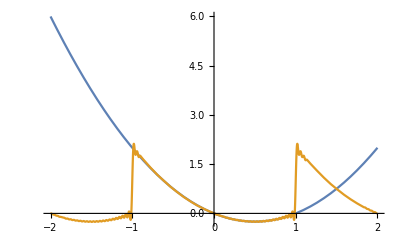

```mathematica
A1n = ExpandAll[∫_-1^1 (x^2-x)Cos[n π x]ⅆx]
A10 =ExpandAll[∫_-1^1 (x^2-x)ⅆx]
B1n =ExpandAll[∫_-1^1 (x^2-x)Sin[n π x]ⅆx]
Plot[{x^2-x, 1/2 A10+∑_(n=1)^50 (A1n * Cos[n π x] + B1n*Sin[n π x])}, {x, -2, 2}]
```

2/(n^2 π^2)+(2 Cos[n π])/(n^2 π^2)-(4 Sin[n π])/(n^3 π^3)

-1/3

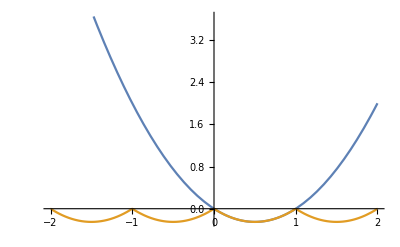

```mathematica
A2n =ExpandAll[2∫_0^1 (x^2-x)Cos[n π x]ⅆx]
A20 =ExpandAll[2∫_0^1 (x^2-x)ⅆx]
Plot[{x^2-x, 1/2 A20+∑_(n=1)^50 (A2n * Cos[n π x])}, {x, -2, 2}]
```

-4/(n^3 π^3)+(4 Cos[n π])/(n^3 π^3)+(2 Sin[n π])/(n^2 π^2)

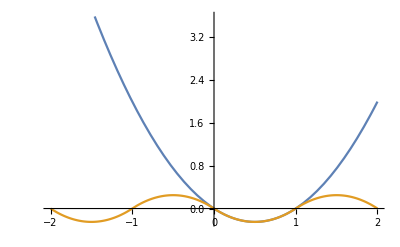

```mathematica
B2n = ExpandAll[2∫_0^1 (x^2-x)Sin[n π x]ⅆx]
Plot[{x^2-x, ∑_(n=1)^50 (B2n * Sin[n π x] )}, {x, -2, 2}]
```